# Лабораторная работа №4 Брич М.Н.

Начальное условие для построения графиков 1a-1c:

```mathematica
xmin:=0;xmax:=10;
ymin:=-1;ymax:=4;
aspRat =(ymax-ymin)/(xmax-xmin);
fXY[x_,y_] := 2-E^(-(x/2-2)^2-(y-2)^2)+2E^(-(x/2-3)^2-(y/3-1)^2);
```

Упражнение 1a

Используемый параметр - PlotRangePadding - метод, задающий отступ внутреннего изображения от границ внешнего графика.
CounturPlot - генерирует контурный график для нескольких переменных

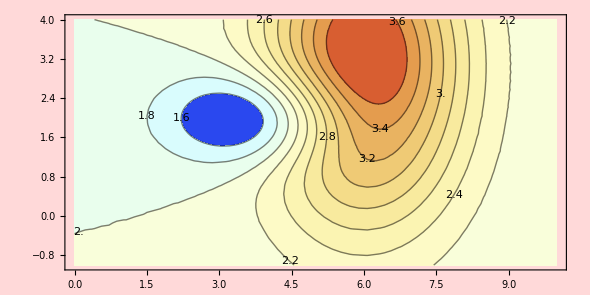

```mathematica
grf2Da = ContourPlot[fXY[x,y],{x,xmin,xmax},{y,ymin,ymax}, (* Передаём функцию и ограничиваем её *)
Contours->11, (* задаёт количество отображаемых контуров на графике *)
ContourLabels->All, (* Включить отображение значений контуров f(x,y) = c *)
ColorFunction->"LightTemperatureMap", (* Устанавливает указанную цветовую карту *)
BaseStyle->12, (* Устанавлеивает стиль - в данном случае текстовых данных *)
AspectRatio->aspRat, (* Устанавливает отношение длины к ширине *)
ImageSize->590, (* Размер изображения *)
PlotRangePadding->{{1,4}, {0,2}}, (* Задаёт отступ от границ внешнего графика {{слева, справа},{снизу, сверху}} *)
Background->LightRed] (* задаёт цвет фона *)
```

Упражнение 1b

Используемый параметр - PlotRegion - метод, задающий отступ графика от границ изображения.
CounturPlot - генерирует контурный график для нескольких переменных

```mathematica
grf2Da = ContourPlot[fXY[x,y],{x,xmin,xmax},{y,ymin,ymax}, (* Передаём функцию и ограничиваем её *)
Contours->11, (* задаёт количество отображаемых контуров на графике *)
ContourLabels->All, (* Включить отображение значений контуров f(x,y) = c *)
ColorFunction->"LightTemperatureMap", (* Устанавливает указанную цветовую карту *)
BaseStyle->12, (* Устанавлеивает стиль - в данном случае текстовых данных *)
AspectRatio->aspRat, (* Устанавливает отношение длины к ширине *)
ImageSize->590, (* Размер изображения *)
PlotRegion->{{0.2,1},{0,0.8}}, (* Отступ графика от границ изображения в процентах {{от слева, до справа},{от снизу, до сверху}} *)
Background->LightRed]  (* фон изображения *)
```

-Graphics-

Упражнение 1c

Метод ContourShading определяет набор цветов для отображения границ контурного графика.
Show - комбинирует графики

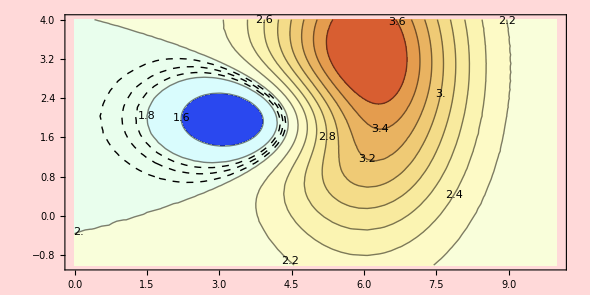

```mathematica
Show[
ContourPlot[fXY[x,y],{x,xmin,xmax},{y,ymin,ymax},Contours->11,ContourLabels->All,ColorFunction->"LightTemperatureMap",BaseStyle->14, AspectRatio->aspRat,ImageSize->590,Background->LightRed],
ContourPlot[fXY[x,y],{x,xmin,xmax},{y,ymin,ymax},Contours->{1.85,1.9,1.95}, (* Отобразить только указанные контуры *)
ContourStyle->Dashed, (* Задать стиль контура пунктирным *)
ContourShading->None, (* Задать набор цветов для отображения контурного графика *)
AspectRatio->aspRat,ImageSize->590]]
```

Упражнение 1d

Метод Inset позволяет вставить почти любой объект с заданием его размеров и местоположения на графике.

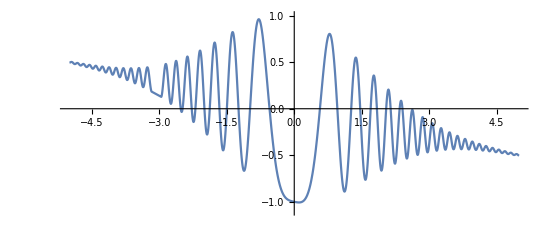

```mathematica
f3[x_]:=(-E^(-0.2*x^2))*Cos[5*x^2]-0.1*x
grf1DdFrgm=Plot[f3[x],{x,-4,-3},AspectRatio->3/7];
Plot[f3[x],{x,-5,5},
AspectRatio->3/7, (* соотношение длины к ширине *)
Epilog->Inset[grf1DdFrgm, (* Epilog указывает, что сначала будет обработан основной график, затем то, что передаётся в эпилог. Inset - Вставляет объект *)
Scaled[{0.05, 0.05}], (*x, y*)
Scaled[{0, 0}],4], (*x,y, размер*)
PlotRange->{-1.1,1}, (* отображает {ymin, ymax} *)
PlotRangeClipping->False, (* не убирает то, что выходит за диапазон *)
ImageSize->550]
```

Упражнение 1e

Hue представляет цвет в цветовом пространстве HSB.

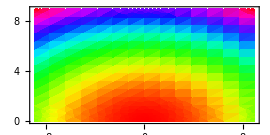
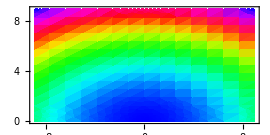

```mathematica
grf2Dd=DensityPlot[x^2+3*y^2,{x,-9,9},{y,0,9}, (* Определяет график плотности *)
BaseStyle->16,AspectRatio->1/2,
PlotLegends->Placed[Automatic,Above], (* Создаёт легенду - шкалу автоматически и отображает её сверху *)
ColorFunction->Hue,(* Задает цветовую гамму *)
ImageSize->270];

grf2De=DensityPlot[x^2+3*y^2,{x,-9,9},{y,0,9},
BaseStyle->16,
AspectRatio->1/2,
PlotLegends->Placed[Automatic,Above],
ColorFunction-> (Hue[2/3 - #]& ), (* смещаем оттенок непрерывного цветового интервала *)
ImageSize->270];

Row[{grf2Dd,grf2De},Spacer[5]]
```